# persistence of memory

I heard once that you should try to look at a clock to see if you can lucid dream.

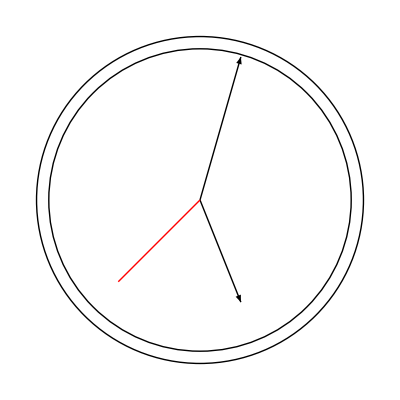

```mathematica
Show[
Graphics@Circle[{0,0},4],
Graphics@Circle[{0,0},3.7],
Graphics@Arrow[{{0,0},{1,-2.5}}],
Graphics[Arrow[{{0,0},{1,3.5}}]],
Graphics[{Red,Line[{{0,0},{-2,-2}}]}]
]
```

I tried it, of course. I’ve never been one to back away from a challenge, no matter how pointless.

And I saw a clock, and saw a time. Oh, it must have been something reasonable, something mundane, not worth noticing, or I certainly would have remembered what time it was when this began.

I know only that I saw a clock, and I stayed in that room, and time passed.

with all hands moving at proper pace

can i use time as a variable? tick some counter up with every second that passes, and use sines and cosines for distances to draw graphics

I don’t remember what time it was, but I don’t think the hands were moving. Or maybe they were. Who can say? Only I would know, and I certainly can’t.

And I know I woke up.

In order to get into a lucid-dreaming state, the test one chooses - looking at a clock, in my case - must become normalized in one’s waking life. So checking clocks again and again had become a nervous habit of sorts, like fidgeting with one’s hair or accessories.

So I checked the clock, upon waking.

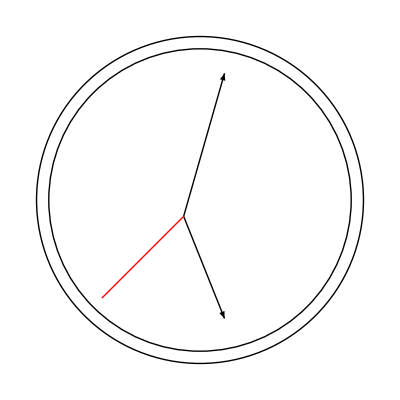

```mathematica
x=-.4;
Show[Graphics@Circle[{0,0},4],
Graphics@Circle[{0,0},3.7],
Graphics@Arrow[{{x,x},{1+x,x+-2.5}}],
Graphics[Arrow[{{x,x},{1+x,x+3.5}}]],
Graphics[{Red,Line[{{x,x},{-2+x,-2+x}}]}]]
```

The strongest impression I have from that first-waking clock was some vague discomfort, the way you feel when you know you’ve left something at home but the cab is already halfway to the airport.

When I know something is wrong, I just know it. And that first-waking clock was wrong.

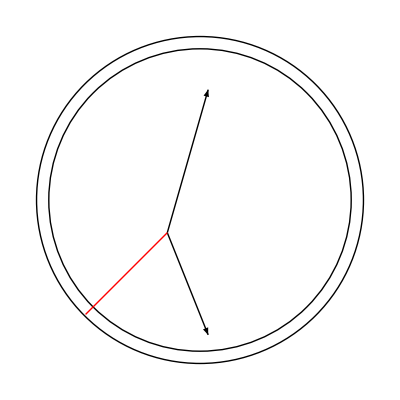

```mathematica
y=-.8;
Show[
Graphics@Circle[{0,0},4],
Graphics@Circle[{0,0},3.7],
Graphics@Arrow[{{y,y},{1+y,y+-2.5}}],
Graphics[Arrow[{{y,y},{1+y,y+3.5}}]],
Graphics[{Red,Line[{{y,y},{-2+y,-2+y}}]}]
]
```

“I’m pretty sure the clock is fucking with me” isn’t a sentence I ever thought I’d think, and now it is the only thing I know is true.

hands drift apart (in directions 0, 2pi/3, 4pi/3) until they hit inner circle

I know only that I woke up, and I am staying in this room until I figure this out, and someday someone might say,

"I heard once that you should try to look at a clock to see if you are awake."

hands start spinning faster; increase by 0.5 rpm every second

# songs of the dead

Dead men tell no tales, it’s true, but some of them definitely wrote their tales down before they died. In written words we know their stories, we know their histories, we know them as they wished to be known.

Or, as they wished certain histories to be known, as the case may be. I aim to know the stories of my ancestors, and possibly tell them in ways we can hear and feel, in the universal language of music.

First, the story as it is told, with numbers marking breaths.

唧唧复唧唧1，木兰当户织2。不闻机杼声3，惟闻女叹息4。问女何所思5，问女何所忆6。女亦无所思，女亦无所忆。昨夜见军帖7，可汗大点兵8。军书十二卷9，卷卷有爷名10。阿爷无大儿，木兰无长兄。愿为市鞍马11，从此替爷征。
东市买骏马，西市买鞍鞯12，南市买辔头13，北市买长鞭。旦辞爷娘去14，暮宿黄河边。不闻爷娘唤女声，但闻黄河流水鸣溅溅15。旦辞黄河去16，暮至黑山头17。不闻爷娘唤女声，但闻燕山胡骑鸣啾啾18。
万里赴戎机，关山度若飞19。朔气传金柝20，寒光照铁衣21。将军百战死，壮士十年归。
归来见天子22，天子坐明堂23。策勋十二转24，赏赐百千强25。可汗问所欲26，木兰不用尚书郎27，愿驰千里足28，送儿还故乡。
爷娘闻女来，出郭相扶将29；阿姊闻妹来30，当户理红妆31；小弟闻姊来，磨刀霍霍向猪羊32。开我东阁门，坐我西阁床。脱我战时袍，著我旧时裳33。当窗理云鬓34，对镜帖花黄35。出门看火伴36，火伴皆惊忙：同行十二年，不知木兰是女郎。
雄兔脚扑朔，雌兔眼迷离37；双兔傍地走，安能辨我是雄雌38

will record self saying this to my satisfaction EVENTUALLY. i always mess up partway through i’ll figure it out

```mathematica
FileNameJoin[{NotebookDirectory[],"myAudio.mp3"}]
```

C:\Users\KyleKeane\Dropbox (MIT)\People\Yiran_Kyle_Shared\myAudio.mp3

```mathematica
beethoven=Import["C:\\Users\\ysh11\\Music\\Music\\1Favorites\\Classical\\Beethoven Piano Concerto #5\\Beethoven - 05 Piano Concerto, 1 Allegro.mp3"]
```

^as an example, of something with definite beats

```mathematica
AudioSampleRate@beethoven
```

44100 Hz

```mathematica
AudioResample[beethoven,8000] (*what does this do*)
```

```mathematica
20*60+40 (*total seconds*)
```

1240

```mathematica
AudioPartition[beethoven,40]
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

can i make them play over each other

also i can’t find the option to bring out harmonics

i just want to play with the thing until it sounds (a) different and (b) maybe aesthetically pleasing

# madmen’s chess

Let’s play a game, just the three of us.

There’s you, the madman agreeing to play this game. There’s the madman assigned to play you, who literally makes moves randomly so long as they are legal and possible. And there’s the real madman, the idiot you’ve chosen to make every nth move for you. If you’re smart, you’ll choose every millionth and play it safe.

If you’re into the spirit of going mad, you’ll choose a number between 2 and 5.

how difficult is this to do? not even visualizing it, assuming a player who can do the “queen’s rook to d5” memory version of playing

should i start with something reasonable like tic-tac-toe?
...how would i even do that

and then move to another game with fewer rules, like checkers

# fairness is a luxury we do not enjoy

https://www2.census.gov/census_2010/03-Demographic_Profile_with_SF1geos/California/

-Graphics-

part 1: teaching gerrymandering. like ^^ that. but interactive? with real places?

```mathematica
CityData[{"SanFrancisco", "California", "UnitedStates"},"Population"]
```

852469 people

okay that took like a solid minute to run, rip

anyway

part 2: the thought is also the comparison of “these large cities in california cumulatively have however many millions of people=2 senators, which is the same population as about 7 of these midwestern states=14 senators, which means in the senate one midwestern person = some fraction of a californian”

can i do population demographics? i don’t see that option but is it hiding from me somehow

the last bit i thought of is defining - like - "a white person = some fraction of a black person re representation in government" if you look at ratio of "x number of black people in the us" vs "y number of white people" and where they are and how many gov reps 

more concretely (and probably clearer explanation): ny has 65.7% white, and 15.9% black. find absolute numbers of each, given ny population of 19.85 million. that means (see below) 5 million black people have 2*15.9% senators, and 9 million white people have 2*65.7% senators.

do that for each state (it looks really gruesome for midwestern states), and add up numbers for total ratio of (race):# senators (can even do for # congress reps, so house + 2; it’s still ugly)

```mathematica
19.85*10^6*.159
```

3.15615×10^6

```mathematica
19.85*^6*.657
```

1.30415×10^7

hopefully to shed some light on how governing can be just where laws are followed, but definitely not fair which is an important distinction to learn

something about systems that need overhauling, and saying “read the constitution” isn’t enough because that was literally written by slaveowners okay

```mathematica
CityData[][[1]]
```

```mathematica
Entity["City",{"Anchorage","Alaska","UnitedStates"}]//EntityProperties
```

{administrative region,number of aggravated assaults,rate of aggravated assault,aggregate home value,aggregate home value, householder 15 to 24 years,aggregate home value, householder 25 to 34 years,aggregate home value, householder 35 to 64 years,aggregate home value, householder 65 years and over,aggregate household income,airport codes,fuel spent in delays,total fuel spent in delays,average annual delay,total annual delay,area,area code,arterial street traffic,arterial street length,average public transit trip distance,number of burglaries,rate of burglary,city sales tax,coordinates,country,county,county sales tax,total rate of crime,total number of crimes,average daily traffic delay,elevation,number of rapes,rate of rape,freeway traffic,freeway length,Gini index,has polygon?,FHFA home price index,FHFA home price index annual average,housing affordability index,households,number of larcenies,rate of larceny,latitude,longitude,total magnetic field strength,median age,median home sale price,median home value,median household income,number of motor vehicle thefts,rate of motor vehicle thefts,incidents of murder and nonnegligent manslaughter,rate of murder and nonnegligent manslaughter,name,next daylight saving shift,nicknames,number of owner-occupied housing units,average daily peak period travelers,peak period travelers per capita,average daily peak period vehicles,notable people born in city,notable people who died in city,per capita income,polygon,city population,population by educational attainment,population by migration in previous 12 months,population by language spoken at home,population by marital status,population by poverty status,population by school enrollment,population density,position,last daylight saving shift,total rate of property crime,total number of property crimes,total public transit use,unlinked public transit trips,4 bedroom apartment fair market rent,1 bedroom apartment fair market rent,3 bedroom apartment fair market rent,2 bedroom apartment fair market rent,studio apartment fair market rent,number of robberies,rate of robbery,daily rush hour length,state sales tax,time zone,total daily traffic delay,total sales tax rate,average peak travel time,unemployment rate,unweighted sample housing units,unweighted sample population,total rate of violent crime,total number of violent crimes,ZIP codes}

## Census

```mathematica
Import["https://www2.census.gov/census_2010/03-Demographic_Profile_with_SF1geos/California/ca20101.dp.zip"]
```

{cageo20101.dp,ca0000120101.dp,ca20101.dp.prd.packinglist.txt}

```mathematica
data=Import["https://www2.census.gov/census_2010/03-Demographic_Profile_with_SF1geos/California/ca20101.dp.zip","cageo20101.dp"];
```

```mathematica
data[[1]]//FullForm
```

List["DPST","CA04000000",14906,403466310059,"20501110720California","A!",37253956,"13680081+37.1485730-119.540651500",1779778]

```mathematica
GeoPosition[Entity["City",{"Sacramento","California","UnitedStates"}]]
```

GeoPosition[{38.5666,-121.469}]

```mathematica
GeoPosition[Entity["AdministrativeDivision",{"California","UnitedStates"}]]
```

GeoPosition[{37.2811,-119.648}]

```mathematica
GeoBubbleChart[{Entity["AdministrativeDivision",{"California","UnitedStates"}]->1,Entity["AdministrativeDivision",{"Oregon","UnitedStates"}]->1},GeoRange->Entity["AdministrativeDivision",{"California","UnitedStates"}]]
```

-Graphics-

kyle couldn’t find centroid, but you should check out 
http://community.wolfram.com/groups/-/m/t/1039049

```mathematica
GeoGraphics[Entity["AdministrativeDivision",{"California","UnitedStates"}]["Polygon"]]
```

-Graphics-

```mathematica
GeoGraphics[GeoMarker@GeoPosition[{37.1485730,-119.540651500}],GeoRange->Entity["AdministrativeDivision",{"California","UnitedStates"}]]
```

-Graphics-

```mathematica
Interpreter["GeoCoordinates"]["37.1485730-119.540651500"]
```

Failure[…]

### another attempt

https://factfinder.census.gov/faces/nav/jsf/pages/index.xhtml 

I have no idea how to scrape data from this. Downloading the CSVs manually doesn’t even help because somehow they’re not useful files

```mathematica
demographicsOrig=Import["C:\\Users\\ysh11\\Documents\\Dropbox (MIT)\\Yiran_Kyle_Shared\\demographics.xlsx"]
```

{{{state,,,,,,,CT,,,,,,,,,,,,ME,,MA,,,,,,,,NH,,,NY,,,,,,,RI,,,,,,VT,,,,,},{total,,,,,,,3.5741×10^6,,,,,,,,,,,,1.32836×10^6,,6.54763×10^6,,,,,,,,1.31647×10^6,,,1.93781×10^7,,,,,,,1.05257×10^6,,,,,,625741.,,,,,},{white,,,,,,,2.77241×10^6,,,,,,,,,,,,1.26497×10^6,,5.26524×10^6,,,,,,,,1.23605×10^6,,,1.2741×10^7,,,,,,,856869.,,,,,,596292.,,,,,},{black,,,,,,,362296.,,,,,,,,,,,,15707.,,434398.,,,,,,,,15035.,,,3.0738×10^6,,,,,,,60189.,,,,,,6277.,,,,,},{reps,9.,3.,11.,6.,55.,9.,7.,3.,29.,16.,4.,4.,20.,11.,6.,6.,8.,8.,4.,10.,11.,16.,10.,6.,10.,3.,5.,6.,4.,14.,5.,29.,15.,3.,18.,7.,7.,20.,4.,9.,3.,11.,38.,6.,3.,13.,12.,5.,10.,3.},{,Alabama,Alaska,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Iowa,Kansas,Kentucky,Louisiana,Maine,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Montana,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,Rhode Island,South Carolina,South Dakota,Tennessee,Texas,Utah,Vermont,Virginia,Washington,West Virginia,Wisconsin,Wyoming},{,7.,1.,9.,4.,53.,7.,5.,1.,27.,14.,2.,2.,18.,9.,4.,4.,6.,6.,2.,8.,9.,14.,8.,4.,8.,1.,3.,4.,2.,12.,3.,27.,13.,1.,16.,5.,5.,18.,2.,7.,1.,9.,36.,4.,1.,11.,10.,3.,8.,1.}}}

```mathematica
MatrixForm@demographicsOrig
```

((state






CT











ME

MA







NH


NY






RI





VT




) | (total






3.5741×10^6











1.32836×10^6

6.54763×10^6







1.31647×10^6


1.93781×10^7






1.05257×10^6





625741.




) | (white






2.77241×10^6











1.26497×10^6

5.26524×10^6







1.23605×10^6


1.2741×10^7






856869.





596292.




) | (black






362296.











15707.

434398.







15035.


3.0738×10^6






60189.





6277.




) | (reps
9.
3.
11.
6.
55.
9.
7.
3.
29.
16.
4.
4.
20.
11.
6.
6.
8.
8.
4.
10.
11.
16.
10.
6.
10.
3.
5.
6.
4.
14.
5.
29.
15.
3.
18.
7.
7.
20.
4.
9.
3.
11.
38.
6.
3.
13.
12.
5.
10.
3.) | (
Alabama
Alaska
Arizona
Arkansas
California
Colorado
Connecticut
Delaware
Florida
Georgia
Hawaii
Idaho
Illinois
Indiana
Iowa
Kansas
Kentucky
Louisiana
Maine
Maryland
Massachusetts
Michigan
Minnesota
Mississippi
Missouri
Montana
Nebraska
Nevada
New Hampshire
New Jersey
New Mexico
New York
North Carolina
North Dakota
Ohio
Oklahoma
Oregon
Pennsylvania
Rhode Island
South Carolina
South Dakota
Tennessee
Texas
Utah
Vermont
Virginia
Washington
West Virginia
Wisconsin
Wyoming) | (
7.
1.
9.
4.
53.
7.
5.
1.
27.
14.
2.
2.
18.
9.
4.
4.
6.
6.
2.
8.
9.
14.
8.
4.
8.
1.
3.
4.
2.
12.
3.
27.
13.
1.
16.
5.
5.
18.
2.
7.
1.
9.
36.
4.
1.
11.
10.
3.
8.
1.))

```mathematica
demographics=Flatten[demographicsOrig,1][[1;;5]]
```

{{state,,,,,,,CT,,,,,,,,,,,,ME,,MA,,,,,,,,NH,,,NY,,,,,,,RI,,,,,,VT,,,,,},{total,,,,,,,3.5741×10^6,,,,,,,,,,,,1.32836×10^6,,6.54763×10^6,,,,,,,,1.31647×10^6,,,1.93781×10^7,,,,,,,1.05257×10^6,,,,,,625741.,,,,,},{white,,,,,,,2.77241×10^6,,,,,,,,,,,,1.26497×10^6,,5.26524×10^6,,,,,,,,1.23605×10^6,,,1.2741×10^7,,,,,,,856869.,,,,,,596292.,,,,,},{black,,,,,,,362296.,,,,,,,,,,,,15707.,,434398.,,,,,,,,15035.,,,3.0738×10^6,,,,,,,60189.,,,,,,6277.,,,,,},{reps,9.,3.,11.,6.,55.,9.,7.,3.,29.,16.,4.,4.,20.,11.,6.,6.,8.,8.,4.,10.,11.,16.,10.,6.,10.,3.,5.,6.,4.,14.,5.,29.,15.,3.,18.,7.,7.,20.,4.,9.,3.,11.,38.,6.,3.,13.,12.,5.,10.,3.}}

```mathematica
MatrixForm@demographics
```

(state |  |  |  |  |  |  | CT |  |  |  |  |  |  |  |  |  |  |  | ME |  | MA |  |  |  |  |  |  |  | NH |  |  | NY |  |  |  |  |  |  | RI |  |  |  |  |  | VT |  |  |  |  | 
total |  |  |  |  |  |  | 3.5741×10^6 |  |  |  |  |  |  |  |  |  |  |  | 1.32836×10^6 |  | 6.54763×10^6 |  |  |  |  |  |  |  | 1.31647×10^6 |  |  | 1.93781×10^7 |  |  |  |  |  |  | 1.05257×10^6 |  |  |  |  |  | 625741. |  |  |  |  | 
white |  |  |  |  |  |  | 2.77241×10^6 |  |  |  |  |  |  |  |  |  |  |  | 1.26497×10^6 |  | 5.26524×10^6 |  |  |  |  |  |  |  | 1.23605×10^6 |  |  | 1.2741×10^7 |  |  |  |  |  |  | 856869. |  |  |  |  |  | 596292. |  |  |  |  | 
black |  |  |  |  |  |  | 362296. |  |  |  |  |  |  |  |  |  |  |  | 15707. |  | 434398. |  |  |  |  |  |  |  | 15035. |  |  | 3.0738×10^6 |  |  |  |  |  |  | 60189. |  |  |  |  |  | 6277. |  |  |  |  | 
reps | 9. | 3. | 11. | 6. | 55. | 9. | 7. | 3. | 29. | 16. | 4. | 4. | 20. | 11. | 6. | 6. | 8. | 8. | 4. | 10. | 11. | 16. | 10. | 6. | 10. | 3. | 5. | 6. | 4. | 14. | 5. | 29. | 15. | 3. | 18. | 7. | 7. | 20. | 4. | 9. | 3. | 11. | 38. | 6. | 3. | 13. | 12. | 5. | 10. | 3.)

percents=table[demographics[[white population]] / total population, black/total]

table[percents[[1,2]] * representatives per state]

# water, water, everywhere - how much of it to drink?

Let’s talk about aquifers!

Oh this is so great there’s WeatherData so we can do

```mathematica
WeatherData["KN23","PrecipitationRate"]
```

$Failed

```mathematica
WeatherData["K04V","PrecipitationAmount"]
```

Missing[NotAvailable]

...or maybe we can’t do that? I wonder why

anyway i wanted to use precipitation to then make a model of

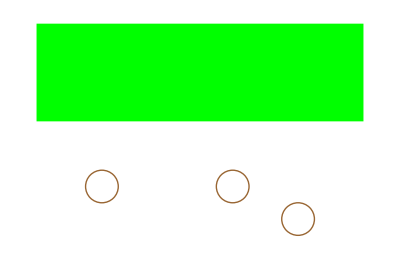

```mathematica
Show[Graphics[{Green, Rectangle[{0,0},{1,.3}]}],
Graphics[{Thick,Brown,Circle[{.2,-.2},.05]}],
Graphics[{Thick,Brown,Circle[{.8,-.3},.05]}],
Graphics[{Thick,Brown,Circle[{.6,-.2},.05]}]]
```

so lots more soil levels - maybe make them a grid instead of individual circles? like Table[coordinates] and make a bunch of circles based on that, i’m positive i’ve done that before and can’t remember how but that’s fine

and investigating soil porosity (shown as density of packing of circles) for given rainfall, to see how aquifers can really be depleted - oh the blue filling also needs to drain at a certain rate to model people’s usage

# defying gravity (at least I’ll try)

Starting in 2016, I believed in superhumans.

Gymnasts have always been physical and mental inspirations, those death- and gravity-defying sixteen-year-olds representing whole nations, and all of humanity is in awe. And they make it look so easy. 

Let’s see how insane they actually are.

https://www.youtube.com/watch?v=yC3zLvDs2AA

is there an easy to identify points of a body and trace

otherwise, manually model three lines? exhausting. probably possible though - find path of ends of lines, draw connecting lines, try not to worry about changing lengths? you can do lines through points, drawing is fine